```mathematica
PhiRD[x_]=9/x^2(Sin[x/Sqrt[3]]/(x/Sqrt[3])-Cos[x/Sqrt[3]]);
PhiRD2[x_]=9/x^2(Cos[x/Sqrt[3]]/(x/Sqrt[3])+Sin[x/Sqrt[3]]);
```

```mathematica
I1RD[u_]=Integrate[4/9 x/xf Cos[x](2 PhiRD[u x]^2+(PhiRD[u x]+u x PhiRD'[u x])^2)//Simplify,{x,0,xf},Assumptions->{xf>0,u>0}];
```

```mathematica
I1RD[u]//ExpToTrig//Simplify
```

1/(16 u^6 xf^5)3 (48 u^2 xf^4-32 u^4 xf^4-432 Cos[xf]+72 xf^2 Cos[xf]-96 u^2 xf^2 Cos[xf]+432 Cos[xf] Cos[(u xf)/(√3)]^2-72 xf^2 Cos[xf] Cos[(u xf)/(√3)]^2-192 u^2 xf^2 Cos[xf] Cos[(u xf)/(√3)]^2+8 (3-2 u^2)^2 xf^4 CosIntegral[xf]-2 (3-2 u^2)^2 xf^4 ExpIntegralEi[1/3 ⅈ (3-2 √3 u) xf]-18 xf^4 ExpIntegralEi[1/3 ⅈ (-3+2 √3 u) xf]+24 u^2 xf^4 ExpIntegralEi[1/3 ⅈ (-3+2 √3 u) xf]-8 u^4 xf^4 ExpIntegralEi[1/3 ⅈ (-3+2 √3 u) xf]-18 xf^4 ExpIntegralEi[-1/3 ⅈ (3+2 √3 u) xf]+24 u^2 xf^4 ExpIntegralEi[-1/3 ⅈ (3+2 √3 u) xf]-8 u^4 xf^4 ExpIntegralEi[-1/3 ⅈ (3+2 √3 u) xf]-18 xf^4 ExpIntegralEi[1/3 ⅈ (3+2 √3 u) xf]+24 u^2 xf^4 ExpIntegralEi[1/3 ⅈ (3+2 √3 u) xf]-8 u^4 xf^4 ExpIntegralEi[1/3 ⅈ (3+2 √3 u) xf]-u^4 xf^4 Log[43046721]-xf^4 Log[150094635296999121]+u^2 xf^4 Log[79766443076872509863361]+9 xf^4 Log[ⅈ-(2 ⅈ u)/(√3)]-12 u^2 xf^4 Log[ⅈ-(2 ⅈ u)/(√3)]+4 u^4 xf^4 Log[ⅈ-(2 ⅈ u)/(√3)]+9 xf^4 Log[-ⅈ+(2 ⅈ u)/(√3)]-12 u^2 xf^4 Log[-ⅈ+(2 ⅈ u)/(√3)]+4 u^4 xf^4 Log[-ⅈ+(2 ⅈ u)/(√3)]-9 xf^4 Log[(3 ⅈ)/(3-2 √3 u)]+12 u^2 xf^4 Log[(3 ⅈ)/(3-2 √3 u)]-4 u^4 xf^4 Log[(3 ⅈ)/(3-2 √3 u)]-9 xf^4 Log[(3 ⅈ)/(-3+2 √3 u)]+12 u^2 xf^4 Log[(3 ⅈ)/(-3+2 √3 u)]-4 u^4 xf^4 Log[(3 ⅈ)/(-3+2 √3 u)]+36 xf^4 Log[3+2 √3 u]-48 u^2 xf^4 Log[3+2 √3 u]+16 u^4 xf^4 Log[3+2 √3 u]+144 xf Sin[xf]-72 xf^3 Sin[xf]+96 u^2 xf^3 Sin[xf]-144 xf Cos[(u xf)/(√3)]^2 Sin[xf]+72 xf^3 Cos[(u xf)/(√3)]^2 Sin[xf]-432 Cos[xf] Sin[(u xf)/(√3)]^2+72 xf^2 Cos[xf] Sin[(u xf)/(√3)]^2+192 u^2 xf^2 Cos[xf] Sin[(u xf)/(√3)]^2+144 xf Sin[xf] Sin[(u xf)/(√3)]^2-72 xf^3 Sin[xf] Sin[(u xf)/(√3)]^2+288 √3 u xf Cos[xf] Sin[(2 u xf)/(√3)]-48 √3 u xf^3 Cos[xf] Sin[(2 u xf)/(√3)]-96 √3 u xf^2 Sin[xf] Sin[(2 u xf)/(√3)])

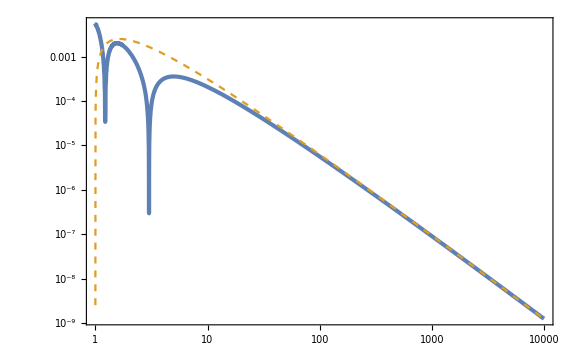

```mathematica
LogLogPlot[{Abs[I1RD[u]]/.{xf->400},(1.35 10^-2)/u^2 Log[u]},{u,1,10^4},PlotStyle->{AbsoluteThickness[3],Dashed}]
```

```mathematica
FullSimplify[Im[Integrate[x PhiRD[u x] PhiRD[v x],x]//ExpToTrig],{u>0,v>0,x>0}]
```

$Aborted